```mathematica
Ps=Table[{i,RandomInteger[5]},{i,1,15}]
```

{{1,5},{2,5},{3,2},{4,3},{5,1},{6,5},{7,4},{8,2},{9,4},{10,0},{11,0},{12,3},{13,4},{14,1},{15,0}}

```mathematica
curves=Table[With[{i=i},(1-3#+2#^2)Ps[[i-1]]+4#(1-#)Ps[[i]]+(-#+2#^2)Ps[[i+1]]&],{i,2,Length@Ps-1}];
```

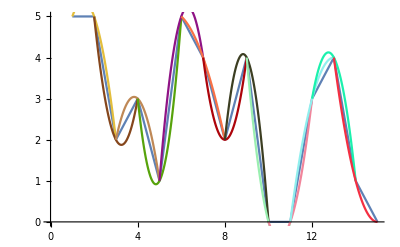

```mathematica
Show[
ListLinePlot[Ps],
ParametricPlot[Evaluate[#[t]&/@curves],{t,0,1},PlotStyle->RandomColor[Length@curves]]
]
```

```mathematica
innerCurves=Table[With[{i=k},Evaluate[(1-2#)curves[[i]][#+0.5]+2# curves[[i+1]][#]&]],{k,1,Length@curves-1}];
```

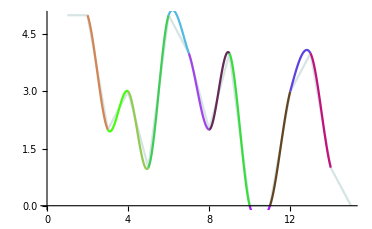

```mathematica
Show[
ListLinePlot[Ps,PlotStyle->Hue[0.5,0.5,0.5,0.21]],
ParametricPlot[Evaluate[#[t]&/@innerCurves],{t,0,0.5},PlotStyle->RandomColor[Length@innerCurves]]
]
```

```mathematica
curves2=Table[With[{i=i},(-4#^3+4#^2-#)Ps[[i-1]]+(12#^3-10#^2+1)Ps[[i]]+(-12#^3+8#^2+#)Ps[[i+1]]+(4#^3-2#^2)Ps[[i+2]]&],{i,2,Length@Ps-2}];
```

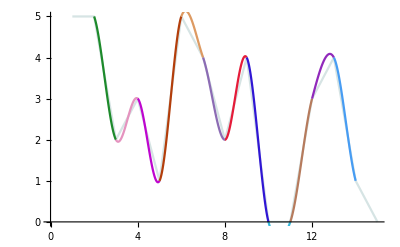

```mathematica
Show[
ListLinePlot[Ps,PlotStyle->Hue[0.5,0.5,0.5,0.21]],
ParametricPlot[Evaluate[#[t]&/@curves2],{t,0,0.5},PlotStyle->RandomColor[Length@innerCurves]]
]
```

```mathematica
Sat
```

```mathematica
img=Import["D:\\assignments\\2023-04-26-Parabola\\version 2\\img\\daijin3bw.png"]
Show[edges=EdgeDetect[img,1.2,0.1],ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
|
```

```mathematica
dcc=DeleteSmallComponents[edges,50]
```

-Graphics-

Part::partd: 部分指定…の長さはオブジェクトの深さを超えています．

(-Graphics-)⟦1⟧

```mathematica
img=Import[NotebookDirectory[]<>"..\\resources\\img1.jpg"]
Show[edges=EdgeDetect[img],ImageSize->Medium]
```

-Graphics-

-Graphics-

```mathematica
mask=Binarize[img,0.9]//ColorNegate
```

```mathematica
Export["mask1.png",mask]
```

mask1.png

```mathematica
(* https://mathematica.stackexchange.com/questions/233092/how-can-i-extract-the-edge-points-from-an-image *)
```

```mathematica
colors=ClusteringComponents[img,Method->{"NeighborhoodContraction", "NeighborhoodRadius"->0.06}]
```

```mathematica
colors[[1]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,3,3,3,3,1,1,3,4,5,6,7,8,9,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,13,14,14,15,15,15,13,13,13,13,10,16,17,17,16,11,12,15,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,18,19,20,8,9,5,21,22,5,8,7,7,7,7,7,7,7,7,8,7,23,23,8,24,19,22,22,22,22,25,19,5,24,26,8,23,23,23,27,23,23,8,26,28,24,20,5,19,19,15,22,22,18,18,22,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,19,19,19,19,19,20,9,23,23,23,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,24,6,6,8,8,6,5,22,18,18,29,30,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,29,31,31,31,31,31,31,29,29,29,29,31,31,29,29,29,29,31,31,29,29,29,29,29,31,31,29,29,21,22,22,19,5,5,20,24,6,9,8,23,23,23,23,23,27,27,27,27,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,28,20,20,5,19,22,22,18,21,29,29,31,31,31,31,31,31,31,31,31,31,29,29,29,29,29,29,31,29,29,29,31,29,29,29,29,29,29,29,29,29,31,31,31,31,31,29,29,29,21,19,20,9,8,23,23,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,20,5,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,32,5,5,5,5,5,5,20,20,20,20,20,5,20,5,5,5,20,20,20,24,6,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,23,23,8,9,10,13,14,14,18,14,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,28,9,9,20,24,24,24,20,24,9,23,8,9,19,18,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,30,15,10,9,8,23,23,23,23,8,24,25,4,21,2,2,1,1,2,1,1,1,1,2,2,1,1,4,4,3,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,3,3,3,1,1,1,1,1,1,1,1,1,3,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2}

```mathematica
dc=DeleteSmallComponents[dcc,10]//Colorize
```

-Graphics-

```mathematica
ifc=ImageForestingComponents[img,0.1]//Colorize
```

ImageForestingComponents::mkinv: 0.1の代りに{1216,756}次元の画像かグラフィックス，またはマーカーを指定する位置のリストが想定されています．

Colorize::invinput: Nullの代りに数値行列または画像が想定されています．

Colorize[Null]

```mathematica
colors//Flatten//Length
```

919296

```mathematica
Times@@(img//ImageDimensions)
```

919296

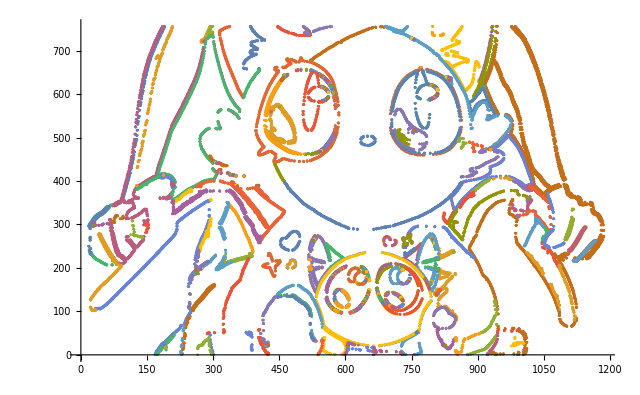
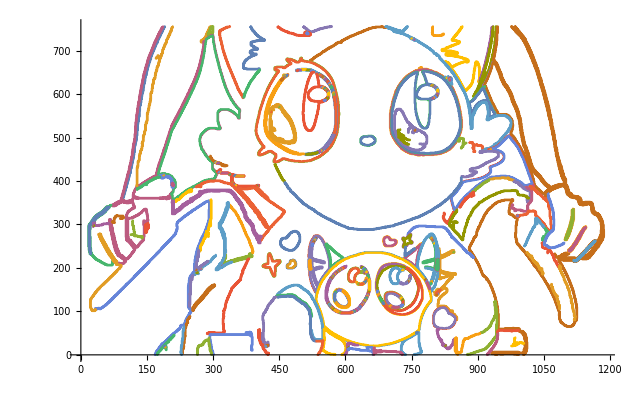

```mathematica
dcdata=Join@@Values[ComponentMeasurements[Binarize@dcc,"Contours",#Count>20&]]/. Line[x_]:>x;
Row[ListPlot[dcdata,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

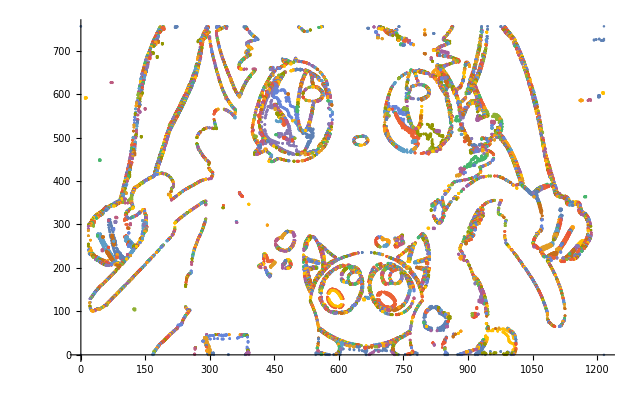
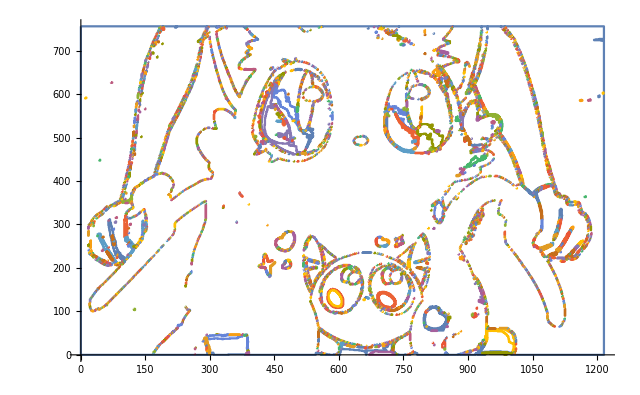

```mathematica
dcdata=Join@@Values[ComponentMeasurements[dc,"Contours",#Count>40&]]/. Line[x_]:>x;
Row[ListPlot[dcdata,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

```mathematica
img=Import["D:\\assignments\\2023-04-26-Parabola\\version 2\\img\\nikukyuu.png"]
```

-Graphics-

```mathematica
Show[edgespaw=EdgeDetect[img,1,0.1],ImageSize->Medium]
```

-Graphics-

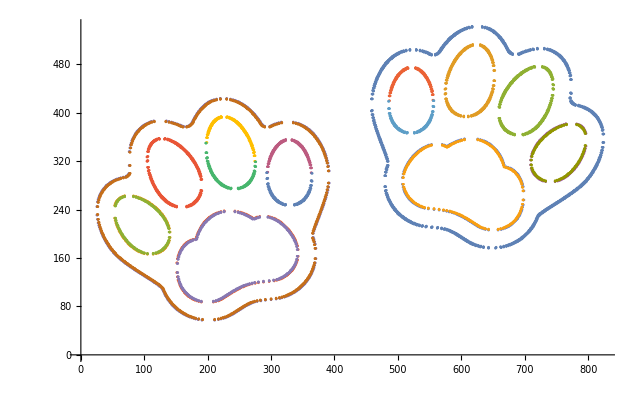
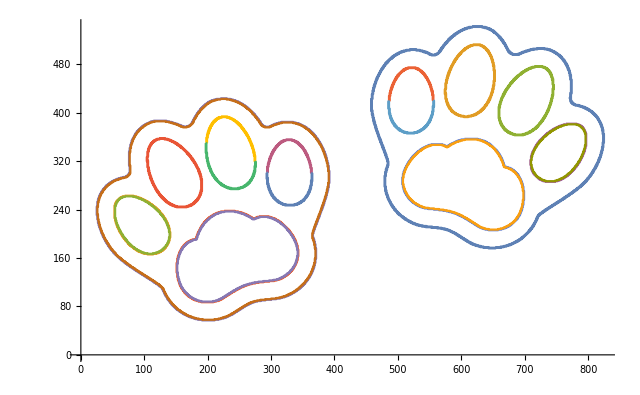

```mathematica
data=Join@@Values[ComponentMeasurements[Binarize@edgespaw,"Contours",#Count>10&]]/. Line[x_]:>x;
Row[ListPlot[data,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

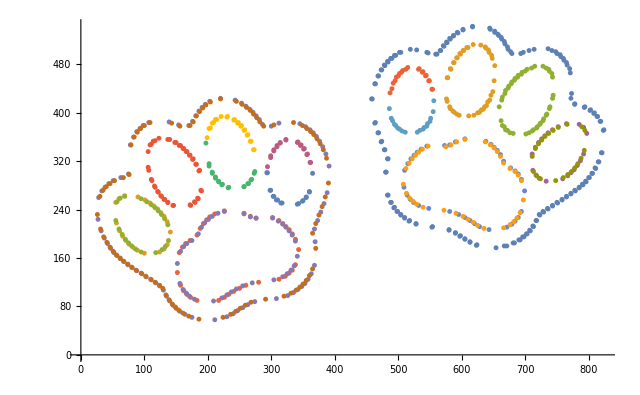
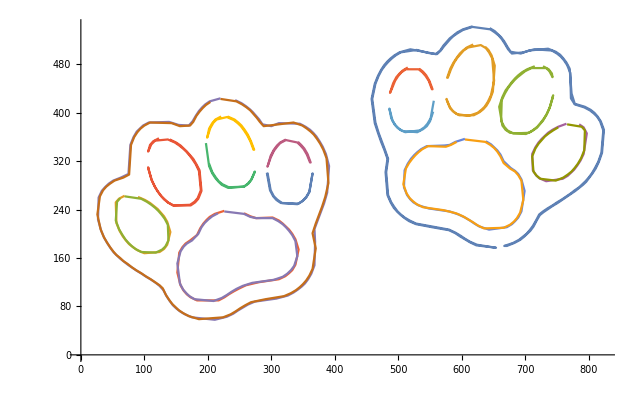

```mathematica
data2=Select[data[[All,1;;;;15]],Length[#]>3&];
Row[ListPlot[data2,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

```mathematica
b=Binarize[img,0.9]
```

-Graphics-

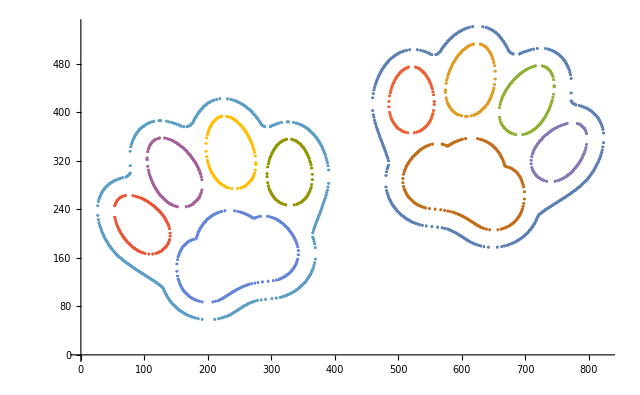
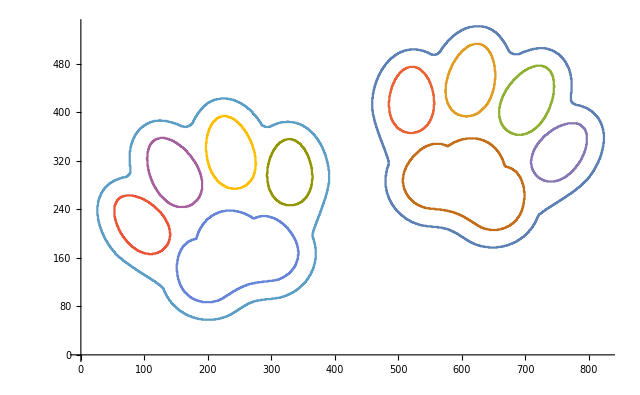

```mathematica
data=Join@@Values[ComponentMeasurements[b,"Contours",#Count>10&]]/. Line[x_]:>x;
Row[ListPlot[data,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

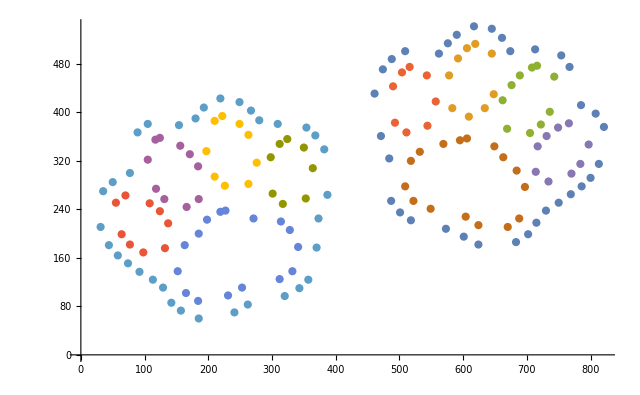
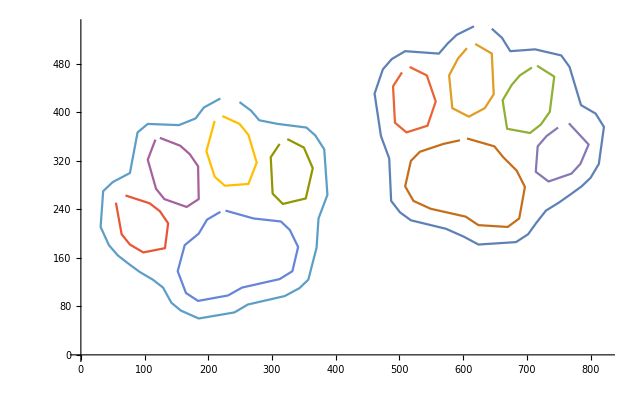

```mathematica
data2=Select[data[[All,1;;;;40]],Length[#]>3&];
Row[ListPlot[data2,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

```mathematica
data=Select[dcdata[[All,1;;;;10]],Length[#]>3&]
```

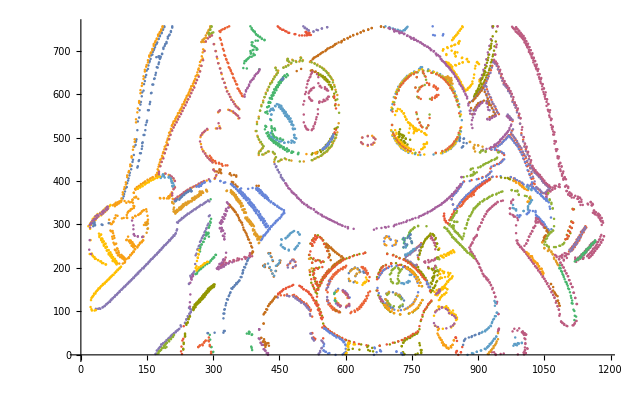
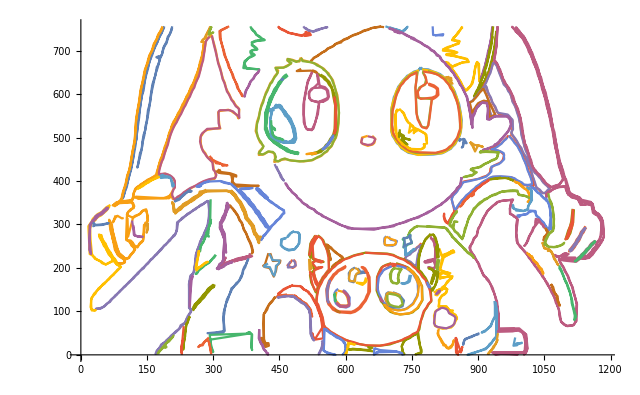

```mathematica
Row[ListPlot[data,Joined->#,ImageSize->{640, 480}]&/@{False,True},Spacer[10]]
```

```mathematica
$stream=OpenWrite["paw.txt",BinaryFormat->True]
```

OutputStream[…]

```mathematica
For[i=1,i<=Length[data],i++,
WriteString[$stream,ToString[Length[data]]<>",-1\n"];
Export[$stream,#&/@data[[i]],"Table","FieldSeparators"->",","TextDelimiters"->""];
WriteString[$stream,"\n"];
]
Close[$stream]
```

paw.txt

```mathematica
$stream=OpenWrite["file.txt",BinaryFormat->True]
```

OutputStream[…]

```mathematica
For[i=1,i<=Length[data],i++,
WriteString[$stream,ToString[Length[data]]<>",-1\n"];
Export[$stream,#&/@data[[i]],"Table","FieldSeparators"->",","TextDelimiters"->""];
WriteString[$stream,"\n"];
]
Close[$stream]
```

file.txt

```mathematica
curves=Table[Table[With[{i=i,k=k},(-4#^3+4#^2-#)data[[k,i-1]]+(12#^3-10#^2+1)data[[k,i]]+(-12#^3+8#^2+#)data[[k,i+1]]+(4#^3-2#^2)data[[k,i+2]]&],{i,2,Length@data[[k]]-2}],{k,1,Length@data}]//Flatten;
```

```mathematica
Length@curves
Length@data
```

3093

136

```mathematica
Show[
ParametricPlot[Evaluate[#[t]&/@curves[[1;;1000]]],{t,0,0.5},PlotStyle->Gray]
]
```

$Aborted